## Odwrócone wahadło o wielu stopniach swobody na wózku

Celem zadania jest wyprowadzenie symbolicznych równań ruchu dla układu wahadła o wielu stopniach swobody osadzonego na ruchomym wózku, przy wykorzystaniu równań Lagrange’a drugiego rodzaju.

Zadanie:
a) Modelowanie geometryczne: Definicja wektorów położeń mas skupionych 𝑚_k w układzie kartezjańskim dla n sztywnych ramion o długościach l_k .
b) Analiza energetyczna: Wyznaczenie energii kinetycznej (E_k) i potencjalnej (E_p) układu jako funkcji współrzędnych uogólnionych q=[x,𝜙_1, ..., 𝜙_n]^T.
c) Wyprowadzenie równań: Sformułowanie Lagranżjanu L=E_k-E_p oraz wygenerowanie układu nieliniowych równań różniczkowych (ODE) z równania Eulera-Lagrange’a.
d) Linearyzacja: Wyznaczenie przybliżonego modelu liniowego wokół górnego punktu równowagi oraz reprezentacji w przestrzeni stanów (StateSpaceModel).
e) Symulacja numeryczna: Rozwiązanie nieliniowego układu równań (NDSolve) dla zadanych warunków początkowych
n=3, 𝜙_k(0)=±π/8
f) Wizualizacja: Wygenerowanie wykresów przebiegów czasowych oraz interaktywnej animacji ruchu układu (Animate).

### Równania Lagrange’ a drugiego rodzaju

ⅆ/ⅆt((∂L)/(∂φ'))-(∂L)/(∂φ)+(∂D)/(∂φ')=τ,
gdzie
	L=E_k-E_p - energia kinetyczna minus energia potencjalna - tzw. potencjał kinetyczny Lagrange’a
	φ - zmienne uogólnione
	D - funkcja dyssypacji Rayleigha (szybkość rozpraszania energii układu)
	τ - siły uogólnione

### Model wahadła

Rozważamy odwrócone wahadło o wielu stopniach swobody umieszczone na wózku przedstawione na rysunku. Zakładamy, że ramiona wahadła są sztywne, pomijamy jednak ich masy. Przyjmujemy
	l[k] - długości ramion,
	m[k] - masy ciężarków,
	m[0] - masa wózka,
	φ[k][t] - kąty pomiędzy ramionami wahadła o osią Y (zmienne uogólnione),
	x[t] - położenie wózka,
	h,w - wymiary wózka,
	f(t) - siła działająca na wózek skierowana wzdłuż osi X.

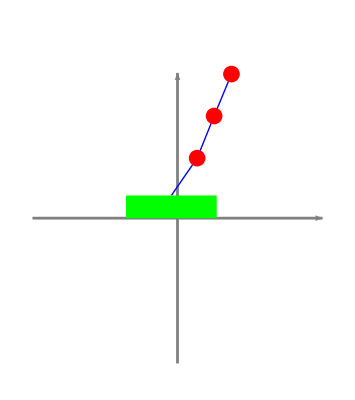

```mathematica
SetOptions[EvaluationNotebook[],CellContext->Notebook];
```

```mathematica
$HistoryLength=10;
```

Liczba ramion n=3

Położenie wózka P_0=(x(t), h)

Położenie końcówek ramion P_k=P_(k-1)+l_k( sin(φ_k(t)), cos(φ_k(t)) )

W celu zapewnienia większej czytelności wyników obliczeń zastosujemy bardziej zwarty sposób zapisu

```mathematica
Format[l[i_Integer]]:=Subscript[l,i];
Format[φ[i_Integer]]:=Subscript[φ,i];
Format[m[i_Integer]]:=Subscript[m,i];
```

Kwadrat prędkości (do wyznaczenia energii kinetycznej

Możemy zabezpieczyć wybrane symbole przed nadaniem im wartości

```mathematica
Protect[P,l,φ,m,V,k,f];
```

Energia kinetyczna

E_k=1/2 m_0 x'(t)^2+1/2∑_(k=1)^n m_k V_k^2

Energia potencjalna
E_p= ∑_(k=1)^n m_k g y_k

Potencjał kinetyczny Lagrange' a

Zdefiniujmy wektor zmiennych uogólnionych

oraz wektory pochodnych zmiennych

Wyznaczymy lewe strony równań Eulera-Lagrange’a
		ⅆ/ⅆt((∂L)/(∂φ'))-(∂L)/(∂φ)+(∂D)/(∂φ')=τ,
	gdzie
		L=E_k-E_p - energia kinetyczna minus energia potencjalna - tzw. potencjał kinetyczny Lagrange’a
		φ - zmienne uogólnione
		D - funkcja dyssypacji Rayleigha (szybkość rozpraszania energii układu)
		τ - siły uogólnione

Gradient można wyznaczyć stosując format Dpaclet:ref/D[f,{{x_1,x_2,…}}]

```mathematica
eq1l//TraditionalForm
```

Budujemy układ równań

Wartości początkowe: 
x[0]==0,
φ_1[0]==π/8,φ_2[0]==π/8,φ_3[0]==π/8,
x'[0]==0,φ_1'[0]==0,φ_2'[0]==0,φ_3'[0]==0

Parametry modelu:
	l_1=l_2=l_3 = 1 [m]
	m_1=m_2=m_3 = 1 [kg]
	g=9.81 [m/s^2]
	h=0.5 [m]
	w=2.0 [m]

Numeryczne rozwiązanie równań ruchu:

Narysujemy trajektorię wózka i końcówek wahadła

### Animacja wahadła

Wykonamy animację układu

Stworzymy prostą funkcję anonimową do rysowania elementów graficznych z zadanym zakresem

```mathematica
show:=(Graphics[#,PlotRange->{{-(n+0.2),(n+0.2)},{-(n+0.2),(n+1)}}]&)
```

```mathematica
{Circle[]//show,show@Circle[]}
```

```mathematica
{Gray,Green,Red,Blue}
```

Osie

```mathematica
(grAxes={GrayLevel[0.5],Thickness[0.005],
Arrow[{{-(n+0.2),0},{(n+0.2),0}}],
Arrow[{{0,-(n+0.2)},{0,(n+0.2)}}]})//show
```

Wózek

```mathematica
grCart[τ_,sol_]:={RGBColor[0, 1, 0],Rectangle[{-w/2+x[t],0},{w/2+x[t],h}]/.par/.sol/.t->τ};
```

```mathematica
{grAxes,grCart[1,sol]}//show
```

```mathematica
grPendulum[t_,sol_]:={ Thick,RGBColor[0, 0, 1],Line[Pv[t,sol]],
PointSize[0.03],RGBColor[1, 0, 0],Point[Pv[t,sol]⟦2;;-1⟧]}
```

```mathematica
grPendulum[0.2,sol]
```

{Thickness[Large],RGBColor[0, 0, 1],Line[{{-0.135352,0.5},{0.433622,1.32236},{0.807521,2.24983},{1.19031,3.17366}}],PointSize[0.03],RGBColor[1, 0, 0],Point[{{0.433622,1.32236},{0.807521,2.24983},{1.19031,3.17366}}]}

```mathematica
show@{grAxes,grCart[0,sol],grPendulum[0,sol]}
```

```mathematica
PendulumPlot[t_,sol_]:=show@{grAxes,grCart[t,sol],grPendulum[t,sol]}
```

```mathematica
PendulumPlot[0.2,sol]
```

```mathematica
Animate[PendulumPlot[t,sol],{t,0,Tsym},AnimationRate->0.5]
```

Możemy zapisać wyniki w pliku “gif”

```mathematica
frames=Table[PendulumPlot[t,sol],{t,0,5,0.1}];
```

```mathematica
SetDirectory@NotebookDirectory[]
Export["invpen.gif",frames]
```

\\filesrv\VPersonaProfiles\kborkowski.GOS\My Documents\cw_5_wahadlo_na_wozku

invpen.gif

```mathematica
iframes=Import["invpen.gif"];
```

```mathematica
ListAnimate[iframes,AnimationRate->5,ImageSize->300,AnimationRate->0.5]
```